first get the diameter of the beam out of c240tme-b on the machine table.

```mathematica
Clear["Global`*"]
mW=10^-3;
uW=10^-6;
um=10^-6;
nm=10^-9;
cm=10^-2;
mm=10^-3;
kHz=10^3;
MHz=10^6;
GHz=10^9;
λ=852nm;
f=8mm;
NA = 0.5;
dia=2 f Tan[ArcSin[NA]];
dia/mm
```

9.2376

assume it’s then focused over a distance f2 into the tweezer. How much power is needed for 10^6 W/m^2 peak intensity ((PRL 92, 033004, 2004))

```mathematica
f2=100cm;
θ=dia/(2f2); (*approx., assuming f2>>dia, also =NA *)
NA2=θ;
w0=λ/(π NA2);




w0=33.um;
"w0="<>ToString[w0/um]<>"um"
(*peak intensity*)
I0=10^6;
P0=1/2 π I0 w0^2;
"P="<>ToString[P0/mW]<>"mW"
zR = (π w0^2)/λ;
"zR="<>ToString[zR/cm]<>"cm"
```

w0=33.um

P=1.7106mW

zR=0.401549cm

```mathematica
w0~f^2
```

## next question. given measured waist and measured power, what is the intensity, rabi rate (for Cs D2) and therefore induced light shift?

```mathematica
P0=66mW;
w0=33um;56um;
λ=852nm;
I0=(2P0)/(π w0^2);

zR=(π w0^2)/λ;
w[z_]:=w0 √(1+(z/zR)^2)
ii[r_,z_]:=I0 (w0/w[z] Exp[-r^2/w[z]^2])^2;


Isat=2.7mW/cm^2;
Γ=5MHz;

Δr=70um;
Δz=.5cm;
Ω=Γ √(ii[Δr,Δz]/(2 Isat)); (*from steck, defn of Ω is -d E0/ ℏ, resonant rabi frequency*)
Δ=(335722-351704.9)GHz; 
Δ=(351722-351704.9)GHz; (*I observed 50-10=40MHz shift of 44'*)

2 Ω^2/Δ/MHz(*eq 15 in https://arxiv.org/pdf/physics/9902072.pdf (optical trap for neutral atoms)--factor of 2 gives transition shift; factor of 1 gives shift of one level only*)
```

24.0432

# look @ power broadening... assuming Isat and Γ similar to atomic values... plot the scattering rate vs detuning in MHz.

```mathematica
P0=66mW;
w0=56um;33um;
λ=852nm;
I0=(2P0)/(π w0^2);

zR=(π w0^2)/λ;
w[z_]:=w0 √(1+(z/zR)^2)
ii[r_,z_]:=I0 (w0/w[z] Exp[-r^2/w[z]^2])^2;


Isat=2.7mW/cm^2;
Γ=5MHz;

Δr=70um;
Δz=.5cm;
Ω=Γ √(ii[Δr,Δz]/(2 Isat)); (*from steck, defn of Ω is -d E0/ ℏ, resonant rabi frequency*)
Δ=(335722-351704.9)GHz; 
Δ=(351722-351704.9)GHz; (*I observed 50-10=40MHz shift of 44'*)

2 Ω^2/Δ/MHz(*eq 15 in https://arxiv.org/pdf/physics/9902072.pdf (optical trap for neutral atoms)--factor of 2 gives transition shift; factor of 1 gives shift of one level only*)
```

43.9336

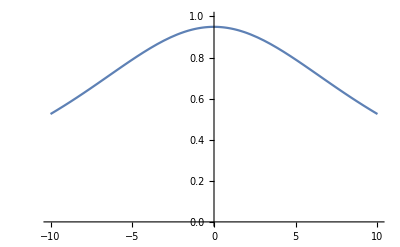

```mathematica
i0=(5uW)/(π w0^2);
Clear[Δ]

Plot[(i0/Isat)/(1+4(Δ MHz/Γ)^2+i0/Isat),{Δ,-10,10},PlotRange->{All,{0,1}}]
```